```mathematica
$Assumptions={_∈Reals,-1<v<1,-L<z<L};
```

```mathematica
Z={xp,yp,zp}
```

{xp,yp,zp}

```mathematica
X={x,y,z};
```

```mathematica
Pos={t,X-Z}//Flatten
```

{t,x-xp,y-yp,z-zp}

```mathematica
B[V_]:=
Module[{mat},
v=Sqrt[V[[1]]^2+V[[2]]^2+V[[3]]^2];
g=1/Sqrt[1-v^2];
mat={{g,-g V[[1]],-g V[[2]],-g V[[3]]},{-g V[[1]], 1+(g-1)V[[1]]^2/v^2,(g-1)V[[1]] V[[2]]/v^2,(g-1)V[[1]] V[[3]]/v^2},{-g V[[2]], (g-1)(V[[1]]V[[2]])/v^2,1+(g-1)V[[2]]^2/v^2,(g-1)V[[2]] V[[3]]/v^2},{-g V[[3]], (g-1)(V[[1]]V[[3]])/v^2,(g-1)(V[[2]]V[[3]])/v^2,1+(g-1)V[[3]]^2/v^2}}
]
```

```mathematica
V={vx,vy,vz};
```

```mathematica
Phif0[X_,t_]=1/Norm[X];
```

```mathematica
posprime=B[V].Pos;
```

```mathematica
(Xprime=posprime[[2;;]])//MatrixForm;
tprime=posprime[[1]];
```

```mathematica
Phifzv=1/Norm[Xprime]//Simplify;
Pifzv=D[Phifzv,t]//Simplify;
Psifxzv=D[Phifzv,x]//Simplify;
Psifyzv=D[Phifzv,y]//Simplify;
Psifzzv=D[Phifzv,z]//Simplify;
```

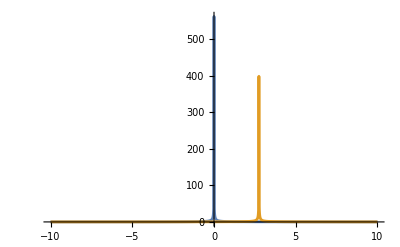

```mathematica
Plot[{Phifzv/.{h->1,t->0,y->0,z->0,
xp->0,yp->0,zp->0,
vx->5/10,vy->0,vz->0},Phifzv/.{h->1,t->5.5,y->0,z->0,
xp->0,yp->0,zp->0,
vx->5/10,vy->0,vz->0}},{x,-10,10},PlotRange->All]
```

```mathematica
Φ=Phifzv/.t->0//Simplify;
Π=Pifzv/.t->0//Simplify;
Ψx=Psifxzv/.t->0//Simplify;
Ψy=Psifyzv/.t->0//Simplify;
Ψz=Psifzzv/.t->0//Simplify;
```

```mathematica
vx D[Π,xp]+vy D[Π,yp]+vz D[Π,zp]-D[Ψx,x]-D[Ψy,y]-D[Ψz,z]//Simplify
```

0

```mathematica
D[Π,x]-vx D[Ψx,xp]-vy D[Ψx,yp]-vz D[Ψx,zp]//Simplify
```

0

```mathematica
DΠdvx=D[Π,vx];
DΠdvy=D[Π,vy];
DΠdvz=D[Π,vz];
```

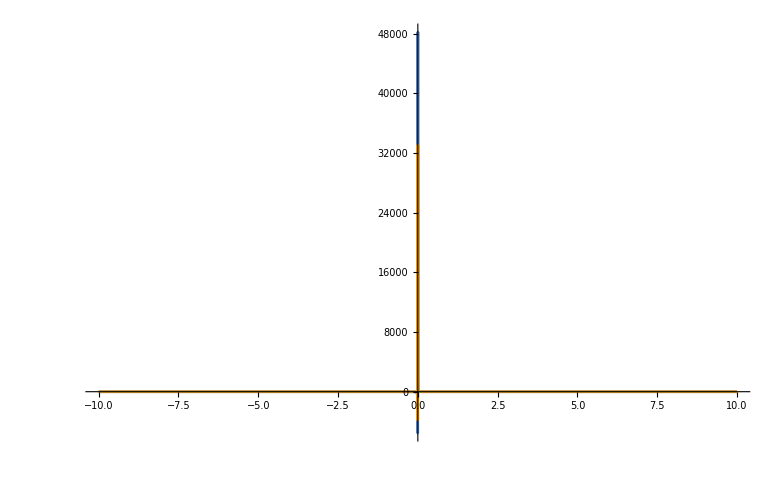

```mathematica
Plot[{Π/.{h->1,y->0,z->0,
xp->0,yp->0,zp->0,
vx->1/10,vy->2/10,vz->3/10},DΠdvz/.{h->1,y->0,z->0,xp->0,yp->0,zp->0,
vx->1/10,vy->2/10,vz->3/10}},{x,-10,10},PlotRange->All]
```

```mathematica
p3=Plot3D[{DΠdvz/.{x->xx,y->yy,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10,h->1}},{xx,-10,10},{yy,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[D[DΠdvy,y]/.{x->xx,y->yy,z->0,
xp->0,yp->0,zp->0,
vx->2/10,vy->2/10,vz->2/10},{xx,-10,10},{yy,-10,10}]
```

-Graphics3D-

```mathematica
c=1/NIntegrate[Exp[-1/(1-x^2)],{x,-1,1}];
ρ[ϵ_][x_]=(c/ϵ)*Piecewise[{{Exp[-ϵ^2/(ϵ^2-x^2)],-ϵ<x<ϵ}}];
```

```mathematica
Plot3D[{ρ[2][x]ρ[2][y]},{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Integrate[ρ[h][x-xx]ρ[h][y-yy]ρ[h][z-zz]DΠdvx/.h->1,{xx,-5,5},{yy,-5,5},{zz,-5,5}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

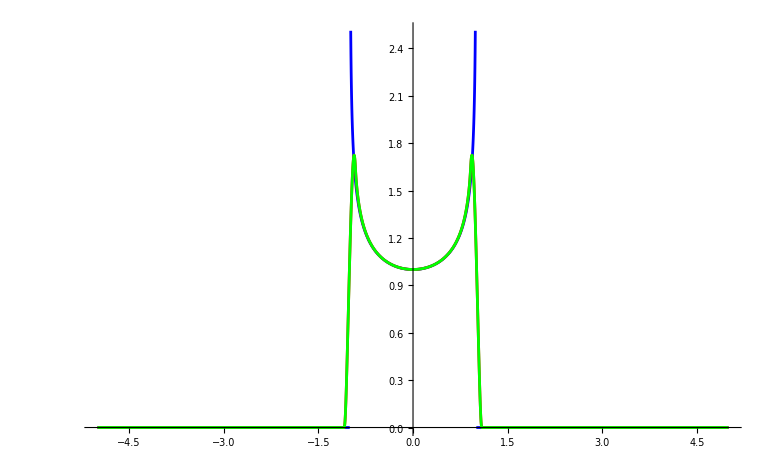

```mathematica
Clear[f,f1,f2,c,ρ,ϵ];
f[x_]=Piecewise[{{0,Abs[x]>=1},{(1-x^2)^(-1/4),Abs[x]<1}}];
c=1/NIntegrate[Exp[-1/(1-x^2)],{x,-1,1}];
ρ[ϵ_][x_]=(c/ϵ)*Piecewise[{{Exp[-ϵ^2/(ϵ^2-x^2)],-ϵ<x<ϵ}}];
f1[ϵ_][x_]:=NIntegrate[ρ[ϵ][x-t]*f[t],{t,-∞,∞}]
f2[ϵ_][x_]:=NIntegrate[ρ[ϵ][t]*f[x-t],{t,-ϵ,ϵ}]
ϵ=.1;
Plot[{f1[ϵ][x]-f2[ϵ][x]},{x,-5,5},PlotStyle->{Blue,Red, Green}]
```